```mathematica
Table[
Sum[StirlingS2[n,k]x^(n-k),{k,0,Infinity}]//Factor,
{n,1,12}]
```

{1,1+x,1+3 x+x^2,1+6 x+7 x^2+x^3,1+10 x+25 x^2+15 x^3+x^4,1+15 x+65 x^2+90 x^3+31 x^4+x^5,1+21 x+140 x^2+350 x^3+301 x^4+63 x^5+x^6,1+28 x+266 x^2+1050 x^3+1701 x^4+966 x^5+127 x^6+x^7,1+36 x+462 x^2+2646 x^3+6951 x^4+7770 x^5+3025 x^6+255 x^7+x^8,1+45 x+750 x^2+5880 x^3+22827 x^4+42525 x^5+34105 x^6+9330 x^7+511 x^8+x^9,1+55 x+1155 x^2+11880 x^3+63987 x^4+179487 x^5+246730 x^6+145750 x^7+28501 x^8+1023 x^9+x^10,1+66 x+1705 x^2+22275 x^3+159027 x^4+627396 x^5+1323652 x^6+1379400 x^7+611501 x^8+86526 x^9+2047 x^10+x^11}

```mathematica
ZetaZero[10]//N
```

0.5+49.7738 ⅈ

```mathematica
RepChromial["C"]
```

{v1x2x3x4x5→24 x-50 x^2+35 x^3-10 x^4+x^5,v12x3x4x5→-6 x+11 x^2-6 x^3+x^4,v13x2x4x5→-6 x+11 x^2-6 x^3+x^4,v14x2x3x5→-6 x+11 x^2-6 x^3+x^4,v15x2x3x4→-6 x+11 x^2-6 x^3+x^4,v1x23x4x5→-6 x+11 x^2-6 x^3+x^4,v1x24x3x5→-6 x+11 x^2-6 x^3+x^4,v1x25x3x4→-6 x+11 x^2-6 x^3+x^4,v1x2x34x5→-6 x+11 x^2-6 x^3+x^4,v1x2x35x4→-6 x+11 x^2-6 x^3+x^4,v1x2x3x45→-6 x+11 x^2-6 x^3+x^4,v123x4x5→2 x-3 x^2+x^3,v124x3x5→2 x-3 x^2+x^3,v125x3x4→2 x-3 x^2+x^3,v12x34x5→2 x-3 x^2+x^3,v12x35x4→2 x-3 x^2+x^3,v12x3x45→2 x-3 x^2+x^3,v134x2x5→2 x-3 x^2+x^3,v135x2x4→2 x-3 x^2+x^3,v13x24x5→2 x-3 x^2+x^3,v13x25x4→2 x-3 x^2+x^3,v13x2x45→2 x-3 x^2+x^3,v145x2x3→2 x-3 x^2+x^3,v14x23x5→2 x-3 x^2+x^3,v14x25x3→2 x-3 x^2+x^3,v14x2x35→2 x-3 x^2+x^3,v15x23x4→2 x-3 x^2+x^3,v15x24x3→2 x-3 x^2+x^3,v15x2x34→2 x-3 x^2+x^3,v1x234x5→2 x-3 x^2+x^3,v1x235x4→2 x-3 x^2+x^3,v1x23x45→2 x-3 x^2+x^3,v1x245x3→2 x-3 x^2+x^3,v1x24x35→2 x-3 x^2+x^3,v1x25x34→2 x-3 x^2+x^3,v1x2x345→2 x-3 x^2+x^3,v1234x5→-x+x^2,v1235x4→-x+x^2,v123x45→-x+x^2,v1245x3→-x+x^2,v124x35→-x+x^2,v125x34→-x+x^2,v12x345→-x+x^2,v1345x2→-x+x^2,v134x25→-x+x^2,v135x24→-x+x^2,v13x245→-x+x^2,v145x23→-x+x^2,v14x235→-x+x^2,v15x234→-x+x^2,v1x2345→-x+x^2,v12345→x}

```mathematica
With[{all=allGraphs2, rep=RepGraph2},
With[{graphs=Table[all[k,"graph"],{k,Keys[all]}]},
MatrixForm[
Table[
Table[all[k,"colofour"]+all[l,"colofour"]/.rep["C"],{l,Keys[all]}],{k,Keys[all]}
], TableHeadings->{graphs, graphs}]
]]
```

( | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 2 -Graphics-2+2 -Graphics-1 | -Graphics-2+2 -Graphics-1 | 2 -Graphics-2+-Graphics-1
-Graphics- | -Graphics-2+2 -Graphics-1 | 2 -Graphics-1 | -Graphics-2+-Graphics-1
-Graphics- | 2 -Graphics-2+-Graphics-1 | -Graphics-2+-Graphics-1 | 2 -Graphics-2)

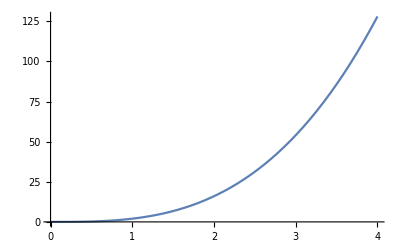
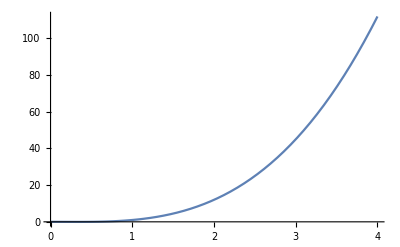
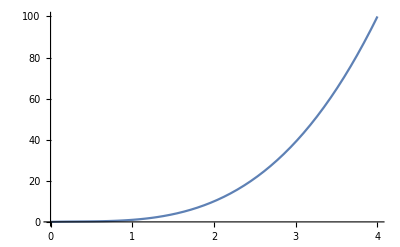
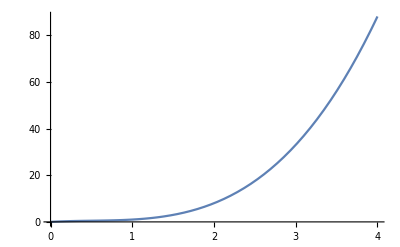
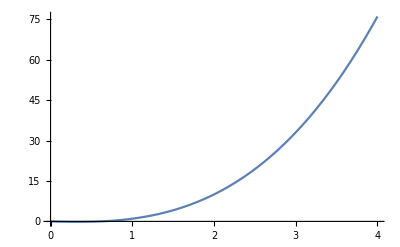
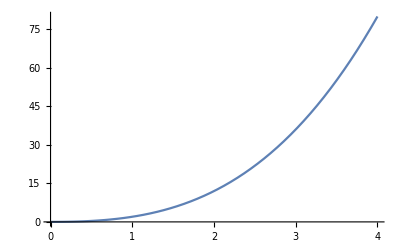
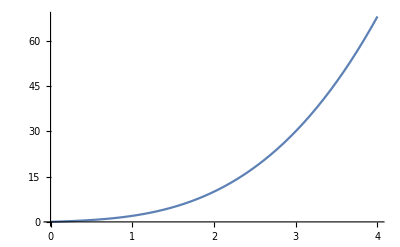
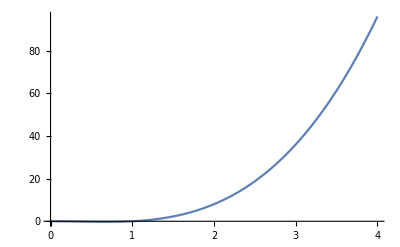
( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-)

```mathematica
With[{all=allGraphs3, rep=RepChromial3},
With[{graphs=Table[all[k,"graph"],{k,Keys[all]}]},
MatrixForm[
Table[
Table[Plot[Expand[all[k,"colofour"]+all[l,"colofour"]/.rep["C"]],{x,0,4}],{l,Keys[all]}],{k,Keys[all]}
], TableHeadings->{graphs, graphs}]
]]
```

```mathematica
With[{all=allGraphs5, rep=RepChromial,max=10},
With[{graphs=Take[Table[all[k,"graph"],{k,Keys[all]}],max]},
MatrixForm[
Table[
Table[Factor[all[k,"colofour"]+all[l,"colofour"]/.rep["C"]],{l,Take [Keys[all],max]}],{k,Take [Keys[all],max]}
], TableHeadings->{graphs, graphs}]
]]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 2 x^5 | x^4 (-1+2 x) | x^3 (1-2 x+2 x^2) | x^2 (-1+2 x) (1-x+x^2) | x (1-4 x+6 x^2-4 x^3+2 x^4) | x (2-7 x+9 x^2-5 x^3+2 x^4) | x (4-12 x+13 x^2-6 x^3+2 x^4) | x (8-20 x+18 x^2-7 x^3+2 x^4) | x (12-28 x+23 x^2-8 x^3+2 x^4) | x (18-39 x+29 x^2-9 x^3+2 x^4)
-Graphics- | x^4 (-1+2 x) | 2 (-1+x) x^4 | (-1+x) x^3 (-1+2 x) | (-1+x) x^2 (1-2 x+2 x^2) | (-1+x) x (-1+2 x) (1-x+x^2) | (-1+x) x (-2+5 x-4 x^2+2 x^3) | (-1+x) x (-4+8 x-5 x^2+2 x^3) | 2 (-1+x)^2 x (4-2 x+x^2) | (-1+x) x (-12+16 x-7 x^2+2 x^3) | (-1+x) x (-18+21 x-8 x^2+2 x^3)
-Graphics- | x^3 (1-2 x+2 x^2) | (-1+x) x^3 (-1+2 x) | 2 (-1+x)^2 x^3 | (-1+x)^2 x^2 (-1+2 x) | (-1+x)^2 x (1-2 x+2 x^2) | (-1+x)^2 x (2-3 x+2 x^2) | 2 (-1+x)^2 x (2-2 x+x^2) | (-1+x) x (-8+12 x-7 x^2+2 x^3) | 2 (-1+x) x (-6+8 x-4 x^2+x^3) | (-1+x) x (-3+2 x) (6-3 x+x^2)
-Graphics- | x^2 (-1+2 x) (1-x+x^2) | (-1+x) x^2 (1-2 x+2 x^2) | (-1+x)^2 x^2 (-1+2 x) | 2 (-1+x)^3 x^2 | (-1+x)^3 x (-1+2 x) | 2 (-1+x)^4 x | (-1+x)^2 x (4-5 x+2 x^2) | (-1+x) x (-8+13 x-8 x^2+2 x^3) | (-1+x) x (-3+2 x) (4-3 x+x^2) | 2 (-1+x) x (-9+11 x-5 x^2+x^3)
-Graphics- | x (1-4 x+6 x^2-4 x^3+2 x^4) | (-1+x) x (-1+2 x) (1-x+x^2) | (-1+x)^2 x (1-2 x+2 x^2) | (-1+x)^3 x (-1+2 x) | 2 (-1+x)^4 x | (-1+x)^3 x (-3+2 x) | (-1+x)^2 x (5-6 x+2 x^2) | (-1+x) x (-3+2 x) (3-3 x+x^2) | (-1+x) x (-13+19 x-10 x^2+2 x^3) | (-1+x) x (-19+24 x-11 x^2+2 x^3)
-Graphics- | x (2-7 x+9 x^2-5 x^3+2 x^4) | (-1+x) x (-2+5 x-4 x^2+2 x^3) | (-1+x)^2 x (2-3 x+2 x^2) | 2 (-1+x)^4 x | (-1+x)^3 x (-3+2 x) | 2 (-2+x) (-1+x)^3 x | (-2+x) (-1+x)^2 x (-3+2 x) | (-2+x) (-1+x) x (5-6 x+2 x^2) | (-2+x) (-1+x) x (7-7 x+2 x^2) | 2 (-2+x) (-1+x) x (5-4 x+x^2)
-Graphics- | x (4-12 x+13 x^2-6 x^3+2 x^4) | (-1+x) x (-4+8 x-5 x^2+2 x^3) | 2 (-1+x)^2 x (2-2 x+x^2) | (-1+x)^2 x (4-5 x+2 x^2) | (-1+x)^2 x (5-6 x+2 x^2) | (-2+x) (-1+x)^2 x (-3+2 x) | 2 (-2+x)^2 (-1+x)^2 x | (-2+x)^2 (-1+x) x (-3+2 x) | 2 (-2+x)^3 (-1+x) x | (-2+x) (-1+x) x (11-9 x+2 x^2)
-Graphics- | x (8-20 x+18 x^2-7 x^3+2 x^4) | 2 (-1+x)^2 x (4-2 x+x^2) | (-1+x) x (-8+12 x-7 x^2+2 x^3) | (-1+x) x (-8+13 x-8 x^2+2 x^3) | (-1+x) x (-3+2 x) (3-3 x+x^2) | (-2+x) (-1+x) x (5-6 x+2 x^2) | (-2+x)^2 (-1+x) x (-3+2 x) | 2 (-2+x)^3 (-1+x) x | (-2+x)^2 (-1+x) x (-5+2 x) | (-2+x) (-1+x) x (13-10 x+2 x^2)
-Graphics- | x (12-28 x+23 x^2-8 x^3+2 x^4) | (-1+x) x (-12+16 x-7 x^2+2 x^3) | 2 (-1+x) x (-6+8 x-4 x^2+x^3) | (-1+x) x (-3+2 x) (4-3 x+x^2) | (-1+x) x (-13+19 x-10 x^2+2 x^3) | (-2+x) (-1+x) x (7-7 x+2 x^2) | 2 (-2+x)^3 (-1+x) x | (-2+x)^2 (-1+x) x (-5+2 x) | 2 (-3+x) (-2+x)^2 (-1+x) x | (-3+x) (-2+x) (-1+x) x (-5+2 x)
-Graphics- | x (18-39 x+29 x^2-9 x^3+2 x^4) | (-1+x) x (-18+21 x-8 x^2+2 x^3) | (-1+x) x (-3+2 x) (6-3 x+x^2) | 2 (-1+x) x (-9+11 x-5 x^2+x^3) | (-1+x) x (-19+24 x-11 x^2+2 x^3) | 2 (-2+x) (-1+x) x (5-4 x+x^2) | (-2+x) (-1+x) x (11-9 x+2 x^2) | (-2+x) (-1+x) x (13-10 x+2 x^2) | (-3+x) (-2+x) (-1+x) x (-5+2 x) | 2 (-3+x)^2 (-2+x) (-1+x) x)

```mathematica
poly=Monitor[
With[{all=allGraphs5, rep=RepChromial},
DeleteDuplicates  [Flatten[Table[
Table[Expand[all[k,"colofour"]+all[l,"colofour"]/.rep["C"]],{l,Select[Sort [Keys[all]],#>=k&]}],{k,Sort [Keys[all]]}
]]]],{k,l}]
```

{2 x^5,-x^4+2 x^5,x^4+x^5,x^3-2 x^4+2 x^5,2 x^3-3 x^4+2 x^5,-x^3+x^4+x^5,x^3+x^5,-x^2+3 x^3-3 x^4+2 x^5,-2 x^2+5 x^3-4 x^4+2 x^5,x^2-2 x^3+x^4+x^5,-3 x^2+6 x^3-4 x^4+2 x^5,-4 x^2+8 x^3-5 x^4+2 x^5,-6 x^2+11 x^3-6 x^4+2 x^5,2 x^2-3 x^3+x^4+x^5,-x^2+x^3+x^5,x^2+x^5,x-4 x^2+6 x^3-4 x^4+2 x^5,2 x-7 x^2+9 x^3-5 x^4+2 x^5,-x+3 x^2-3 x^3+x^4+x^5,3 x-9 x^2+10 x^3-5 x^4+2 x^5,4 x-12 x^2+13 x^3-6 x^4+2 x^5,6 x-17 x^2+17 x^3-7 x^4+2 x^5,-2 x+5 x^2-4 x^3+x^4+x^5,x-2 x^2+x^3+x^5,7 x-17 x^2+15 x^3-6 x^4+2 x^5,8 x-20 x^2+18 x^3-7 x^4+2 x^5,4 x-10 x^2+10 x^3-5 x^4+2 x^5,6 x-15 x^2+14 x^3-6 x^4+2 x^5,10 x-23 x^2+19 x^3-7 x^4+2 x^5,12 x-28 x^2+23 x^3-8 x^4+2 x^5,-3 x+6 x^2-4 x^3+x^4+x^5,-4 x+8 x^2-5 x^3+x^4+x^5,14 x-31 x^2+24 x^3-8 x^4+2 x^5,18 x-39 x^2+29 x^3-9 x^4+2 x^5,24 x-50 x^2+35 x^3-10 x^4+2 x^5,-6 x+11 x^2-6 x^3+x^4+x^5,2 x-3 x^2+x^3+x^5,-x+x^2+x^5,x+x^5,-2 x^4+2 x^5,x^5,x^3-3 x^4+2 x^5,2 x^3-4 x^4+2 x^5,-x^3+x^5,x^3-x^4+x^5,-x^2+3 x^3-4 x^4+2 x^5,-2 x^2+5 x^3-5 x^4+2 x^5,x^2-2 x^3+x^5,-3 x^2+6 x^3-5 x^4+2 x^5,-4 x^2+8 x^3-6 x^4+2 x^5,-6 x^2+11 x^3-7 x^4+2 x^5,2 x^2-3 x^3+x^5,-x^2+x^3-x^4+x^5,x^2-x^4+x^5,x-4 x^2+6 x^3-5 x^4+2 x^5,2 x-7 x^2+9 x^3-6 x^4+2 x^5,-x+3 x^2-3 x^3+x^5,3 x-9 x^2+10 x^3-6 x^4+2 x^5,4 x-12 x^2+13 x^3-7 x^4+2 x^5,6 x-17 x^2+17 x^3-8 x^4+2 x^5,-2 x+5 x^2-4 x^3+x^5,x-2 x^2+x^3-x^4+x^5,7 x-17 x^2+15 x^3-7 x^4+2 x^5,8 x-20 x^2+18 x^3-8 x^4+2 x^5,4 x-10 x^2+10 x^3-6 x^4+2 x^5,6 x-15 x^2+14 x^3-7 x^4+2 x^5,10 x-23 x^2+19 x^3-8 x^4+2 x^5,12 x-28 x^2+23 x^3-9 x^4+2 x^5,-3 x+6 x^2-4 x^3+x^5,-4 x+8 x^2-5 x^3+x^5,14 x-31 x^2+24 x^3-9 x^4+2 x^5,18 x-39 x^2+29 x^3-10 x^4+2 x^5,24 x-50 x^2+35 x^3-11 x^4+2 x^5,-6 x+11 x^2-6 x^3+x^5,2 x-3 x^2+x^3-x^4+x^5,-x+x^2-x^4+x^5,x-x^4+x^5,2 x^4,2 x^3-2 x^4+x^5,-x^3+2 x^4,x^3+x^4,-x^2+3 x^3-2 x^4+x^5,-2 x^2+5 x^3-3 x^4+x^5,x^2-2 x^3+2 x^4,-3 x^2+6 x^3-3 x^4+x^5,-4 x^2+8 x^3-4 x^4+x^5,-6 x^2+11 x^3-5 x^4+x^5,2 x^2-3 x^3+2 x^4,-x^2+x^3+x^4,x^2+x^4,x-4 x^2+6 x^3-3 x^4+x^5,2 x-7 x^2+9 x^3-4 x^4+x^5,-x+3 x^2-3 x^3+2 x^4,3 x-9 x^2+10 x^3-4 x^4+x^5,4 x-12 x^2+13 x^3-5 x^4+x^5,6 x-17 x^2+17 x^3-6 x^4+x^5,-2 x+5 x^2-4 x^3+2 x^4,x-2 x^2+x^3+x^4,7 x-17 x^2+15 x^3-5 x^4+x^5,8 x-20 x^2+18 x^3-6 x^4+x^5,4 x-10 x^2+10 x^3-4 x^4+x^5,6 x-15 x^2+14 x^3-5 x^4+x^5,10 x-23 x^2+19 x^3-6 x^4+x^5,12 x-28 x^2+23 x^3-7 x^4+x^5,-3 x+6 x^2-4 x^3+2 x^4,-4 x+8 x^2-5 x^3+2 x^4,14 x-31 x^2+24 x^3-7 x^4+x^5,18 x-39 x^2+29 x^3-8 x^4+x^5,24 x-50 x^2+35 x^3-9 x^4+x^5,-6 x+11 x^2-6 x^3+2 x^4,2 x-3 x^2+x^3+x^4,-x+x^2+x^4,x+x^4,3 x^3-5 x^4+2 x^5,-x^4+x^5,-x^2+4 x^3-5 x^4+2 x^5,-2 x^2+6 x^3-6 x^4+2 x^5,x^2-x^3-x^4+x^5,-3 x^2+7 x^3-6 x^4+2 x^5,-4 x^2+9 x^3-7 x^4+2 x^5,-6 x^2+12 x^3-8 x^4+2 x^5,2 x^2-2 x^3-x^4+x^5,-x^2+2 x^3-2 x^4+x^5,x^2+x^3-2 x^4+x^5,x-4 x^2+7 x^3-6 x^4+2 x^5,2 x-7 x^2+10 x^3-7 x^4+2 x^5,-x+3 x^2-2 x^3-x^4+x^5,3 x-9 x^2+11 x^3-7 x^4+2 x^5,4 x-12 x^2+14 x^3-8 x^4+2 x^5,6 x-17 x^2+18 x^3-9 x^4+2 x^5,-2 x+5 x^2-3 x^3-x^4+x^5,x-2 x^2+2 x^3-2 x^4+x^5,7 x-17 x^2+16 x^3-8 x^4+2 x^5,8 x-20 x^2+19 x^3-9 x^4+2 x^5,4 x-10 x^2+11 x^3-7 x^4+2 x^5,6 x-15 x^2+15 x^3-8 x^4+2 x^5,10 x-23 x^2+20 x^3-9 x^4+2 x^5,12 x-28 x^2+24 x^3-10 x^4+2 x^5,-3 x+6 x^2-3 x^3-x^4+x^5,-4 x+8 x^2-4 x^3-x^4+x^5,14 x-31 x^2+25 x^3-10 x^4+2 x^5,18 x-39 x^2+30 x^3-11 x^4+2 x^5,24 x-50 x^2+36 x^3-12 x^4+2 x^5,-6 x+11 x^2-5 x^3-x^4+x^5,2 x-3 x^2+2 x^3-2 x^4+x^5,-x+x^2+x^3-2 x^4+x^5,x+x^3-2 x^4+x^5,4 x^3-6 x^4+2 x^5,x^3-2 x^4+x^5,3 x^3-3 x^4+x^5,-x^2+5 x^3-6 x^4+2 x^5,-2 x^2+7 x^3-7 x^4+2 x^5,x^2-2 x^4+x^5,-3 x^2+8 x^3-7 x^4+2 x^5,-4 x^2+10 x^3-8 x^4+2 x^5,-6 x^2+13 x^3-9 x^4+2 x^5,2 x^2-x^3-2 x^4+x^5,-x^2+3 x^3-3 x^4+x^5,x^2+2 x^3-3 x^4+x^5,x-4 x^2+8 x^3-7 x^4+2 x^5,2 x-7 x^2+11 x^3-8 x^4+2 x^5,-x+3 x^2-x^3-2 x^4+x^5,3 x-9 x^2+12 x^3-8 x^4+2 x^5,4 x-12 x^2+15 x^3-9 x^4+2 x^5,6 x-17 x^2+19 x^3-10 x^4+2 x^5,-2 x+5 x^2-2 x^3-2 x^4+x^5,x-2 x^2+3 x^3-3 x^4+x^5,7 x-17 x^2+17 x^3-9 x^4+2 x^5,8 x-20 x^2+20 x^3-10 x^4+2 x^5,4 x-10 x^2+12 x^3-8 x^4+2 x^5,6 x-15 x^2+16 x^3-9 x^4+2 x^5,10 x-23 x^2+21 x^3-10 x^4+2 x^5,12 x-28 x^2+25 x^3-11 x^4+2 x^5,-3 x+6 x^2-2 x^3-2 x^4+x^5,-4 x+8 x^2-3 x^3-2 x^4+x^5,14 x-31 x^2+26 x^3-11 x^4+2 x^5,18 x-39 x^2+31 x^3-12 x^4+2 x^5,24 x-50 x^2+37 x^3-13 x^4+2 x^5,-6 x+11 x^2-4 x^3-2 x^4+x^5,2 x-3 x^2+3 x^3-3 x^4+x^5,-x+x^2+2 x^3-3 x^4+x^5,x+2 x^3-3 x^4+x^5,-2 x^3+2 x^4,x^4,-2 x^2+4 x^3-3 x^4+x^5,x^2-3 x^3+2 x^4,-3 x^2+5 x^3-3 x^4+x^5,-4 x^2+7 x^3-4 x^4+x^5,-6 x^2+10 x^3-5 x^4+x^5,2 x^2-4 x^3+2 x^4,-x^2+x^4,x^2-x^3+x^4,x-4 x^2+5 x^3-3 x^4+x^5,2 x-7 x^2+8 x^3-4 x^4+x^5,-x+3 x^2-4 x^3+2 x^4,3 x-9 x^2+9 x^3-4 x^4+x^5,4 x-12 x^2+12 x^3-5 x^4+x^5,6 x-17 x^2+16 x^3-6 x^4+x^5,-2 x+5 x^2-5 x^3+2 x^4,x-2 x^2+x^4,7 x-17 x^2+14 x^3-5 x^4+x^5,8 x-20 x^2+17 x^3-6 x^4+x^5,4 x-10 x^2+9 x^3-4 x^4+x^5,6 x-15 x^2+13 x^3-5 x^4+x^5,10 x-23 x^2+18 x^3-6 x^4+x^5,12 x-28 x^2+22 x^3-7 x^4+x^5,-3 x+6 x^2-5 x^3+2 x^4,-4 x+8 x^2-6 x^3+2 x^4,14 x-31 x^2+23 x^3-7 x^4+x^5,18 x-39 x^2+28 x^3-8 x^4+x^5,24 x-50 x^2+34 x^3-9 x^4+x^5,-6 x+11 x^2-7 x^3+2 x^4,2 x-3 x^2+x^4,-x+x^2-x^3+x^4,x-x^3+x^4,2 x^3,-x^2+4 x^3-3 x^4+x^5,-2 x^2+6 x^3-4 x^4+x^5,-3 x^2+7 x^3-4 x^4+x^5,-4 x^2+9 x^3-5 x^4+x^5,-6 x^2+12 x^3-6 x^4+x^5,2 x^2-2 x^3+x^4,-x^2+2 x^3,x^2+x^3,x-4 x^2+7 x^3-4 x^4+x^5,2 x-7 x^2+10 x^3-5 x^4+x^5,-x+3 x^2-2 x^3+x^4,3 x-9 x^2+11 x^3-5 x^4+x^5,4 x-12 x^2+14 x^3-6 x^4+x^5,6 x-17 x^2+18 x^3-7 x^4+x^5,-2 x+5 x^2-3 x^3+x^4,x-2 x^2+2 x^3,7 x-17 x^2+16 x^3-6 x^4+x^5,8 x-20 x^2+19 x^3-7 x^4+x^5,4 x-10 x^2+11 x^3-5 x^4+x^5,6 x-15 x^2+15 x^3-6 x^4+x^5,10 x-23 x^2+20 x^3-7 x^4+x^5,12 x-28 x^2+24 x^3-8 x^4+x^5,-3 x+6 x^2-3 x^3+x^4,-4 x+8 x^2-4 x^3+x^4,14 x-31 x^2+25 x^3-8 x^4+x^5,18 x-39 x^2+30 x^3-9 x^4+x^5,24 x-50 x^2+36 x^3-10 x^4+x^5,-6 x+11 x^2-5 x^3+x^4,2 x-3 x^2+2 x^3,-x+x^2+x^3,x+x^3,-5 x^2+11 x^3-8 x^4+2 x^5,-7 x^2+14 x^3-9 x^4+2 x^5,x-5 x^2+9 x^3-7 x^4+2 x^5,2 x-8 x^2+12 x^3-8 x^4+2 x^5,-x+2 x^2-2 x^4+x^5,3 x-10 x^2+13 x^3-8 x^4+2 x^5,4 x-13 x^2+16 x^3-9 x^4+2 x^5,6 x-18 x^2+20 x^3-10 x^4+2 x^5,-2 x+4 x^2-x^3-2 x^4+x^5,x-3 x^2+4 x^3-3 x^4+x^5,7 x-18 x^2+18 x^3-9 x^4+2 x^5,8 x-21 x^2+21 x^3-10 x^4+2 x^5,4 x-11 x^2+13 x^3-8 x^4+2 x^5,6 x-16 x^2+17 x^3-9 x^4+2 x^5,10 x-24 x^2+22 x^3-10 x^4+2 x^5,12 x-29 x^2+26 x^3-11 x^4+2 x^5,-3 x+5 x^2-x^3-2 x^4+x^5,-4 x+7 x^2-2 x^3-2 x^4+x^5,14 x-32 x^2+27 x^3-11 x^4+2 x^5,18 x-40 x^2+32 x^3-12 x^4+2 x^5,24 x-51 x^2+38 x^3-13 x^4+2 x^5,-6 x+10 x^2-3 x^3-2 x^4+x^5,2 x-4 x^2+4 x^3-3 x^4+x^5,-x+3 x^3-3 x^4+x^5,x-x^2+3 x^3-3 x^4+x^5,-8 x^2+16 x^3-10 x^4+2 x^5,2 x^3-3 x^4+x^5,-3 x^2+6 x^3-4 x^4+x^5,-x^2+5 x^3-4 x^4+x^5,x-6 x^2+11 x^3-8 x^4+2 x^5,2 x-9 x^2+14 x^3-9 x^4+2 x^5,3 x-11 x^2+15 x^3-9 x^4+2 x^5,4 x-14 x^2+18 x^3-10 x^4+2 x^5,6 x-19 x^2+22 x^3-11 x^4+2 x^5,-2 x+3 x^2+x^3-3 x^4+x^5,x-4 x^2+6 x^3-4 x^4+x^5,7 x-19 x^2+20 x^3-10 x^4+2 x^5,8 x-22 x^2+23 x^3-11 x^4+2 x^5,10 x-25 x^2+24 x^3-11 x^4+2 x^5,12 x-30 x^2+28 x^3-12 x^4+2 x^5,-3 x+4 x^2+x^3-3 x^4+x^5,-4 x+6 x^2-3 x^4+x^5,14 x-33 x^2+29 x^3-12 x^4+2 x^5,18 x-41 x^2+34 x^3-13 x^4+2 x^5,24 x-52 x^2+40 x^3-14 x^4+2 x^5,-6 x+9 x^2-x^3-3 x^4+x^5,2 x-5 x^2+6 x^3-4 x^4+x^5,-x-x^2+5 x^3-4 x^4+x^5,x-2 x^2+5 x^3-4 x^4+x^5,-5 x^2+9 x^3-5 x^4+x^5,3 x^2-5 x^3+2 x^4,-x^3+x^4,2 x-6 x^2+7 x^3-4 x^4+x^5,-x+4 x^2-5 x^3+2 x^4,3 x-8 x^2+8 x^3-4 x^4+x^5,4 x-11 x^2+11 x^3-5 x^4+x^5,6 x-16 x^2+15 x^3-6 x^4+x^5,-2 x+6 x^2-6 x^3+2 x^4,x-x^2-x^3+x^4,7 x-16 x^2+13 x^3-5 x^4+x^5,8 x-19 x^2+16 x^3-6 x^4+x^5,4 x-9 x^2+8 x^3-4 x^4+x^5,6 x-14 x^2+12 x^3-5 x^4+x^5,10 x-22 x^2+17 x^3-6 x^4+x^5,12 x-27 x^2+21 x^3-7 x^4+x^5,-3 x+7 x^2-6 x^3+2 x^4,-4 x+9 x^2-7 x^3+2 x^4,14 x-30 x^2+22 x^3-7 x^4+x^5,18 x-38 x^2+27 x^3-8 x^4+x^5,24 x-49 x^2+33 x^3-9 x^4+x^5,-6 x+12 x^2-8 x^3+2 x^4,2 x-2 x^2-x^3+x^4,-x+2 x^2-2 x^3+x^4,x+x^2-2 x^3+x^4,-9 x^2+17 x^3-10 x^4+2 x^5,x-7 x^2+12 x^3-8 x^4+2 x^5,2 x-10 x^2+15 x^3-9 x^4+2 x^5,3 x-12 x^2+16 x^3-9 x^4+2 x^5,4 x-15 x^2+19 x^3-10 x^4+2 x^5,6 x-20 x^2+23 x^3-11 x^4+2 x^5,-2 x+2 x^2+2 x^3-3 x^4+x^5,x-5 x^2+7 x^3-4 x^4+x^5,7 x-20 x^2+21 x^3-10 x^4+2 x^5,8 x-23 x^2+24 x^3-11 x^4+2 x^5,10 x-26 x^2+25 x^3-11 x^4+2 x^5,12 x-31 x^2+29 x^3-12 x^4+2 x^5,-3 x+3 x^2+2 x^3-3 x^4+x^5,-4 x+5 x^2+x^3-3 x^4+x^5,14 x-34 x^2+30 x^3-12 x^4+2 x^5,18 x-42 x^2+35 x^3-13 x^4+2 x^5,24 x-53 x^2+41 x^3-14 x^4+2 x^5,-6 x+8 x^2-3 x^4+x^5,-x-2 x^2+6 x^3-4 x^4+x^5,x-3 x^2+6 x^3-4 x^4+x^5,-10 x^2+19 x^3-11 x^4+2 x^5,-2 x^2+5 x^3-4 x^4+x^5,-3 x^2+8 x^3-5 x^4+x^5,x-8 x^2+14 x^3-9 x^4+2 x^5,2 x-11 x^2+17 x^3-10 x^4+2 x^5,3 x-13 x^2+18 x^3-10 x^4+2 x^5,4 x-16 x^2+21 x^3-11 x^4+2 x^5,6 x-21 x^2+25 x^3-12 x^4+2 x^5,-2 x+x^2+4 x^3-4 x^4+x^5,x-6 x^2+9 x^3-5 x^4+x^5,7 x-21 x^2+23 x^3-11 x^4+2 x^5,8 x-24 x^2+26 x^3-12 x^4+2 x^5,10 x-27 x^2+27 x^3-12 x^4+2 x^5,12 x-32 x^2+31 x^3-13 x^4+2 x^5,-3 x+2 x^2+4 x^3-4 x^4+x^5,-4 x+4 x^2+3 x^3-4 x^4+x^5,14 x-35 x^2+32 x^3-13 x^4+2 x^5,18 x-43 x^2+37 x^3-14 x^4+2 x^5,24 x-54 x^2+43 x^3-15 x^4+2 x^5,-6 x+7 x^2+2 x^3-4 x^4+x^5,2 x-7 x^2+9 x^3-5 x^4+x^5,-x-3 x^2+8 x^3-5 x^4+x^5,x-4 x^2+8 x^3-5 x^4+x^5,-12 x^2+22 x^3-12 x^4+2 x^5,-4 x^2+8 x^3-5 x^4+x^5,-7 x^2+12 x^3-6 x^4+x^5,-5 x^2+11 x^3-6 x^4+x^5,x-10 x^2+17 x^3-10 x^4+2 x^5,2 x-13 x^2+20 x^3-11 x^4+2 x^5,3 x-15 x^2+21 x^3-11 x^4+2 x^5,4 x-18 x^2+24 x^3-12 x^4+2 x^5,6 x-23 x^2+28 x^3-13 x^4+2 x^5,-2 x-x^2+7 x^3-5 x^4+x^5,x-8 x^2+12 x^3-6 x^4+x^5,7 x-23 x^2+26 x^3-12 x^4+2 x^5,8 x-26 x^2+29 x^3-13 x^4+2 x^5,10 x-29 x^2+30 x^3-13 x^4+2 x^5,12 x-34 x^2+34 x^3-14 x^4+2 x^5,-3 x+7 x^3-5 x^4+x^5,-4 x+2 x^2+6 x^3-5 x^4+x^5,14 x-37 x^2+35 x^3-14 x^4+2 x^5,18 x-45 x^2+40 x^3-15 x^4+2 x^5,24 x-56 x^2+46 x^3-16 x^4+2 x^5,-6 x+5 x^2+5 x^3-5 x^4+x^5,2 x-9 x^2+12 x^3-6 x^4+x^5,-x-5 x^2+11 x^3-6 x^4+x^5,x-6 x^2+11 x^3-6 x^4+x^5,4 x^2-6 x^3+2 x^4,x^2-2 x^3+x^4,3 x^2-3 x^3+x^4,-x+5 x^2-6 x^3+2 x^4,3 x-7 x^2+7 x^3-4 x^4+x^5,4 x-10 x^2+10 x^3-5 x^4+x^5,6 x-15 x^2+14 x^3-6 x^4+x^5,-2 x+7 x^2-7 x^3+2 x^4,x-2 x^3+x^4,7 x-15 x^2+12 x^3-5 x^4+x^5,8 x-18 x^2+15 x^3-6 x^4+x^5,4 x-8 x^2+7 x^3-4 x^4+x^5,6 x-13 x^2+11 x^3-5 x^4+x^5,10 x-21 x^2+16 x^3-6 x^4+x^5,12 x-26 x^2+20 x^3-7 x^4+x^5,-3 x+8 x^2-7 x^3+2 x^4,-4 x+10 x^2-8 x^3+2 x^4,14 x-29 x^2+21 x^3-7 x^4+x^5,18 x-37 x^2+26 x^3-8 x^4+x^5,24 x-48 x^2+32 x^3-9 x^4+x^5,-6 x+13 x^2-9 x^3+2 x^4,2 x-x^2-2 x^3+x^4,-x+3 x^2-3 x^3+x^4,x+2 x^2-3 x^3+x^4,-2 x^2+2 x^3,x^3,2 x-8 x^2+10 x^3-5 x^4+x^5,3 x-10 x^2+11 x^3-5 x^4+x^5,4 x-13 x^2+14 x^3-6 x^4+x^5,6 x-18 x^2+18 x^3-7 x^4+x^5,-2 x+4 x^2-3 x^3+x^4,x-3 x^2+2 x^3,7 x-18 x^2+16 x^3-6 x^4+x^5,8 x-21 x^2+19 x^3-7 x^4+x^5,10 x-24 x^2+20 x^3-7 x^4+x^5,12 x-29 x^2+24 x^3-8 x^4+x^5,-3 x+5 x^2-3 x^3+x^4,-4 x+7 x^2-4 x^3+x^4,14 x-32 x^2+25 x^3-8 x^4+x^5,18 x-40 x^2+30 x^3-9 x^4+x^5,24 x-51 x^2+36 x^3-10 x^4+x^5,-6 x+10 x^2-5 x^3+x^4,2 x-4 x^2+2 x^3,-x+x^3,x-x^2+x^3,2 x^2,2 x-6 x^2+9 x^3-5 x^4+x^5,-x+4 x^2-3 x^3+x^4,3 x-8 x^2+10 x^3-5 x^4+x^5,4 x-11 x^2+13 x^3-6 x^4+x^5,6 x-16 x^2+17 x^3-7 x^4+x^5,-2 x+6 x^2-4 x^3+x^4,7 x-16 x^2+15 x^3-6 x^4+x^5,8 x-19 x^2+18 x^3-7 x^4+x^5,4 x-9 x^2+10 x^3-5 x^4+x^5,6 x-14 x^2+14 x^3-6 x^4+x^5,10 x-22 x^2+19 x^3-7 x^4+x^5,12 x-27 x^2+23 x^3-8 x^4+x^5,-3 x+7 x^2-4 x^3+x^4,-4 x+9 x^2-5 x^3+x^4,14 x-30 x^2+24 x^3-8 x^4+x^5,18 x-38 x^2+29 x^3-9 x^4+x^5,24 x-49 x^2+35 x^3-10 x^4+x^5,-6 x+12 x^2-6 x^3+x^4,2 x-2 x^2+x^3,-x+2 x^2,x+x^2,5 x-16 x^2+19 x^3-10 x^4+2 x^5,9 x-24 x^2+24 x^3-11 x^4+2 x^5,5 x-14 x^2+16 x^3-9 x^4+2 x^5,11 x-27 x^2+25 x^3-11 x^4+2 x^5,13 x-32 x^2+29 x^3-12 x^4+2 x^5,15 x-35 x^2+30 x^3-12 x^4+2 x^5,19 x-43 x^2+35 x^3-13 x^4+2 x^5,25 x-54 x^2+41 x^3-14 x^4+2 x^5,-5 x+7 x^2-3 x^4+x^5,2 x-4 x^2+6 x^3-4 x^4+x^5,3 x-9 x^2+10 x^3-5 x^4+x^5,16 x-38 x^2+33 x^3-13 x^4+2 x^5,20 x-46 x^2+38 x^3-14 x^4+2 x^5,26 x-57 x^2+44 x^3-15 x^4+2 x^5,3 x-7 x^2+9 x^3-5 x^4+x^5,5 x-14 x^2+14 x^3-6 x^4+x^5,7 x-17 x^2+15 x^3-6 x^4+x^5,5 x-12 x^2+11 x^3-5 x^4+x^5,9 x-20 x^2+16 x^3-6 x^4+x^5,11 x-25 x^2+20 x^3-7 x^4+x^5,-5 x+11 x^2-8 x^3+2 x^4,13 x-28 x^2+21 x^3-7 x^4+x^5,17 x-36 x^2+26 x^3-8 x^4+x^5,23 x-47 x^2+32 x^3-9 x^4+x^5,-7 x+14 x^2-9 x^3+2 x^4,9 x-26 x^2+27 x^3-12 x^4+2 x^5,11 x-29 x^2+28 x^3-12 x^4+2 x^5,15 x-37 x^2+33 x^3-13 x^4+2 x^5,17 x-40 x^2+34 x^3-13 x^4+2 x^5,21 x-48 x^2+39 x^3-14 x^4+2 x^5,27 x-59 x^2+45 x^3-15 x^4+2 x^5,16 x-40 x^2+36 x^3-14 x^4+2 x^5,22 x-51 x^2+42 x^3-15 x^4+2 x^5,28 x-62 x^2+48 x^3-16 x^4+2 x^5,3 x-11 x^2+13 x^3-6 x^4+x^5,5 x-12 x^2+13 x^3-6 x^4+x^5,4 x-12 x^2+13 x^3-6 x^4+x^5,7 x-19 x^2+18 x^3-7 x^4+x^5,13 x-34 x^2+32 x^3-13 x^4+2 x^5,20 x-48 x^2+41 x^3-15 x^4+2 x^5,30 x-67 x^2+52 x^3-17 x^4+2 x^5,-6 x^2+11 x^3-6 x^4+x^5,8 x-20 x^2+18 x^3-7 x^4+x^5,5 x-16 x^2+17 x^3-7 x^4+x^5,7 x-17 x^2+17 x^3-7 x^4+x^5,10 x-23 x^2+19 x^3-7 x^4+x^5,16 x-34 x^2+25 x^3-8 x^4+x^5,22 x-45 x^2+31 x^3-9 x^4+x^5,-8 x+16 x^2-10 x^3+2 x^4,2 x^2-3 x^3+x^4,-3 x+6 x^2-4 x^3+x^4,-x+5 x^2-4 x^3+x^4,9 x-22 x^2+19 x^3-7 x^4+x^5,13 x-30 x^2+24 x^3-8 x^4+x^5,15 x-33 x^2+25 x^3-8 x^4+x^5,19 x-41 x^2+30 x^3-9 x^4+x^5,25 x-52 x^2+36 x^3-10 x^4+x^5,-5 x+9 x^2-5 x^3+x^4,3 x-5 x^2+2 x^3,-x^2+x^3,19 x-45 x^2+38 x^3-14 x^4+2 x^5,25 x-56 x^2+44 x^3-15 x^4+2 x^5,31 x-67 x^2+50 x^3-16 x^4+2 x^5,8 x-17 x^2+15 x^3-6 x^4+x^5,26 x-59 x^2+47 x^3-16 x^4+2 x^5,32 x-70 x^2+53 x^3-17 x^4+2 x^5,9 x-20 x^2+18 x^3-7 x^4+x^5,22 x-49 x^2+39 x^3-14 x^4+2 x^5,28 x-60 x^2+45 x^3-15 x^4+2 x^5,5 x-10 x^2+10 x^3-5 x^4+x^5,30 x-65 x^2+49 x^3-16 x^4+2 x^5,7 x-15 x^2+14 x^3-6 x^4+x^5,34 x-73 x^2+54 x^3-17 x^4+2 x^5,11 x-23 x^2+19 x^3-7 x^4+x^5,36 x-78 x^2+58 x^3-18 x^4+2 x^5,6 x-17 x^2+17 x^3-7 x^4+x^5,14 x-31 x^2+24 x^3-8 x^4+x^5,11 x-27 x^2+23 x^3-8 x^4+x^5,13 x-28 x^2+23 x^3-8 x^4+x^5,21 x-44 x^2+31 x^3-9 x^4+x^5,-9 x+17 x^2-10 x^3+2 x^4,20 x-42 x^2+30 x^3-9 x^4+x^5,-10 x+19 x^2-11 x^3+2 x^4,-2 x+5 x^2-4 x^3+x^4,-3 x+8 x^2-5 x^3+x^4,38 x-81 x^2+59 x^3-18 x^4+2 x^5,15 x-31 x^2+24 x^3-8 x^4+x^5,42 x-89 x^2+64 x^3-19 x^4+2 x^5,12 x-28 x^2+23 x^3-8 x^4+x^5,17 x-38 x^2+29 x^3-9 x^4+x^5,19 x-39 x^2+29 x^3-9 x^4+x^5,48 x-100 x^2+70 x^3-20 x^4+2 x^5,18 x-39 x^2+29 x^3-9 x^4+x^5,26 x-53 x^2+36 x^3-10 x^4+x^5,23 x-49 x^2+35 x^3-10 x^4+x^5,25 x-50 x^2+35 x^3-10 x^4+x^5,-12 x+22 x^2-12 x^3+2 x^4,-4 x+8 x^2-5 x^3+x^4,-7 x+12 x^2-6 x^3+x^4,-5 x+11 x^2-6 x^3+x^4,4 x-6 x^2+2 x^3,x-2 x^2+x^3,3 x-3 x^2+x^3,-2 x+2 x^2,x^2,2 x}

```mathematica
Map[CompleteBaseCoeff[#]&, poly]//Sort//MatrixPlot
```

-Graphics-

```mathematica
poly2=Monitor[
With[{all=allGraphs5, rep=RepChromial},
DeleteDuplicates  [Flatten[Table[
Table[Expand[all[k,"colofour"]*all[l,"colofour"]/.rep["C"]],{l,Select[Sort [Keys[all]],#>=k&]}],{k,Sort [Keys[all]]}
]]]],{IntegerDigits[k,3],IntegerDigits[l,3]}]
```

{x^10,-x^9+x^10,x^9,x^8-2 x^9+x^10,2 x^8-3 x^9+x^10,-x^8+x^9,x^8,-x^7+3 x^8-3 x^9+x^10,-2 x^7+5 x^8-4 x^9+x^10,x^7-2 x^8+x^9,-3 x^7+6 x^8-4 x^9+x^10,-4 x^7+8 x^8-5 x^9+x^10,-6 x^7+11 x^8-6 x^9+x^10,2 x^7-3 x^8+x^9,-x^7+x^8,x^7,x^6-4 x^7+6 x^8-4 x^9+x^10,2 x^6-7 x^7+9 x^8-5 x^9+x^10,-x^6+3 x^7-3 x^8+x^9,3 x^6-9 x^7+10 x^8-5 x^9+x^10,4 x^6-12 x^7+13 x^8-6 x^9+x^10,6 x^6-17 x^7+17 x^8-7 x^9+x^10,-2 x^6+5 x^7-4 x^8+x^9,x^6-2 x^7+x^8,7 x^6-17 x^7+15 x^8-6 x^9+x^10,8 x^6-20 x^7+18 x^8-7 x^9+x^10,4 x^6-10 x^7+10 x^8-5 x^9+x^10,6 x^6-15 x^7+14 x^8-6 x^9+x^10,10 x^6-23 x^7+19 x^8-7 x^9+x^10,12 x^6-28 x^7+23 x^8-8 x^9+x^10,-3 x^6+6 x^7-4 x^8+x^9,-4 x^6+8 x^7-5 x^8+x^9,14 x^6-31 x^7+24 x^8-8 x^9+x^10,18 x^6-39 x^7+29 x^8-9 x^9+x^10,24 x^6-50 x^7+35 x^8-10 x^9+x^10,-6 x^6+11 x^7-6 x^8+x^9,2 x^6-3 x^7+x^8,-x^6+x^7,x^6,-x^5+5 x^6-10 x^7+10 x^8-5 x^9+x^10,-2 x^5+9 x^6-16 x^7+14 x^8-6 x^9+x^10,x^5-4 x^6+6 x^7-4 x^8+x^9,-3 x^5+12 x^6-19 x^7+15 x^8-6 x^9+x^10,-4 x^5+16 x^6-25 x^7+19 x^8-7 x^9+x^10,-6 x^5+23 x^6-34 x^7+24 x^8-8 x^9+x^10,2 x^5-7 x^6+9 x^7-5 x^8+x^9,-x^5+3 x^6-3 x^7+x^8,-7 x^5+24 x^6-32 x^7+21 x^8-7 x^9+x^10,-8 x^5+28 x^6-38 x^7+25 x^8-8 x^9+x^10,-4 x^5+14 x^6-20 x^7+15 x^8-6 x^9+x^10,-6 x^5+21 x^6-29 x^7+20 x^8-7 x^9+x^10,-10 x^5+33 x^6-42 x^7+26 x^8-8 x^9+x^10,-12 x^5+40 x^6-51 x^7+31 x^8-9 x^9+x^10,3 x^5-9 x^6+10 x^7-5 x^8+x^9,4 x^5-12 x^6+13 x^7-6 x^8+x^9,-14 x^5+45 x^6-55 x^7+32 x^8-9 x^9+x^10,-18 x^5+57 x^6-68 x^7+38 x^8-10 x^9+x^10,-24 x^5+74 x^6-85 x^7+45 x^8-11 x^9+x^10,6 x^5-17 x^6+17 x^7-7 x^8+x^9,-2 x^5+5 x^6-4 x^7+x^8,x^5-2 x^6+x^7,-x^5+x^6,7 x^5-17 x^6+15 x^7-6 x^8+x^9,8 x^5-20 x^6+18 x^7-7 x^8+x^9,4 x^5-10 x^6+10 x^7-5 x^8+x^9,6 x^5-15 x^6+14 x^7-6 x^8+x^9,10 x^5-23 x^6+19 x^7-7 x^8+x^9,12 x^5-28 x^6+23 x^7-8 x^8+x^9,-3 x^5+6 x^6-4 x^7+x^8,-4 x^5+8 x^6-5 x^7+x^8,14 x^5-31 x^6+24 x^7-8 x^8+x^9,18 x^5-39 x^6+29 x^7-9 x^8+x^9,24 x^5-50 x^6+35 x^7-10 x^8+x^9,-6 x^5+11 x^6-6 x^7+x^8,2 x^5-3 x^6+x^7,x^5,x^4-6 x^5+15 x^6-20 x^7+15 x^8-6 x^9+x^10,2 x^4-11 x^5+25 x^6-30 x^7+20 x^8-7 x^9+x^10,-x^4+5 x^5-10 x^6+10 x^7-5 x^8+x^9,3 x^4-15 x^5+31 x^6-34 x^7+21 x^8-7 x^9+x^10,4 x^4-20 x^5+41 x^6-44 x^7+26 x^8-8 x^9+x^10,6 x^4-29 x^5+57 x^6-58 x^7+32 x^8-9 x^9+x^10,-2 x^4+9 x^5-16 x^6+14 x^7-6 x^8+x^9,x^4-4 x^5+6 x^6-4 x^7+x^8,7 x^4-31 x^5+56 x^6-53 x^7+28 x^8-8 x^9+x^10,8 x^4-36 x^5+66 x^6-63 x^7+33 x^8-9 x^9+x^10,4 x^4-18 x^5+34 x^6-35 x^7+21 x^8-7 x^9+x^10,6 x^4-27 x^5+50 x^6-49 x^7+27 x^8-8 x^9+x^10,10 x^4-43 x^5+75 x^6-68 x^7+34 x^8-9 x^9+x^10,12 x^4-52 x^5+91 x^6-82 x^7+40 x^8-10 x^9+x^10,-3 x^4+12 x^5-19 x^6+15 x^7-6 x^8+x^9,-4 x^4+16 x^5-25 x^6+19 x^7-7 x^8+x^9,14 x^4-59 x^5+100 x^6-87 x^7+41 x^8-10 x^9+x^10,18 x^4-75 x^5+125 x^6-106 x^7+48 x^8-11 x^9+x^10,24 x^4-98 x^5+159 x^6-130 x^7+56 x^8-12 x^9+x^10,-6 x^4+23 x^5-34 x^6+24 x^7-8 x^8+x^9,2 x^4-7 x^5+9 x^6-5 x^7+x^8,-x^4+3 x^5-3 x^6+x^7,x^4-2 x^5+x^6,14 x^4-55 x^5+88 x^6-74 x^7+35 x^8-9 x^9+x^10,16 x^4-64 x^5+104 x^6-88 x^7+41 x^8-10 x^9+x^10,8 x^4-32 x^5+54 x^6-50 x^7+27 x^8-8 x^9+x^10,12 x^4-48 x^5+79 x^6-69 x^7+34 x^8-9 x^9+x^10,20 x^4-76 x^5+117 x^6-94 x^7+42 x^8-10 x^9+x^10,24 x^4-92 x^5+142 x^6-113 x^7+49 x^8-11 x^9+x^10,-6 x^4+21 x^5-29 x^6+20 x^7-7 x^8+x^9,-8 x^4+28 x^5-38 x^6+25 x^7-8 x^8+x^9,28 x^4-104 x^5+155 x^6-119 x^7+50 x^8-11 x^9+x^10,36 x^4-132 x^5+193 x^6-144 x^7+58 x^8-12 x^9+x^10,48 x^4-172 x^5+244 x^6-175 x^7+67 x^8-13 x^9+x^10,-12 x^4+40 x^5-51 x^6+31 x^7-9 x^8+x^9,4 x^4-12 x^5+13 x^6-6 x^7+x^8,-2 x^4+5 x^5-4 x^6+x^7,2 x^4-3 x^5+x^6,-7 x^4+24 x^5-32 x^6+21 x^7-7 x^8+x^9,-4 x^4+14 x^5-20 x^6+15 x^7-6 x^8+x^9,-10 x^4+33 x^5-42 x^6+26 x^7-8 x^8+x^9,3 x^4-9 x^5+10 x^6-5 x^7+x^8,-14 x^4+45 x^5-55 x^6+32 x^7-9 x^8+x^9,-18 x^4+57 x^5-68 x^6+38 x^7-10 x^8+x^9,-24 x^4+74 x^5-85 x^6+45 x^7-11 x^8+x^9,6 x^4-17 x^5+17 x^6-7 x^7+x^8,-x^4+x^5,7 x^4-17 x^5+15 x^6-6 x^7+x^8,8 x^4-20 x^5+18 x^6-7 x^7+x^8,4 x^4-10 x^5+10 x^6-5 x^7+x^8,6 x^4-15 x^5+14 x^6-6 x^7+x^8,10 x^4-23 x^5+19 x^6-7 x^7+x^8,12 x^4-28 x^5+23 x^6-8 x^7+x^8,-3 x^4+6 x^5-4 x^6+x^7,-4 x^4+8 x^5-5 x^6+x^7,14 x^4-31 x^5+24 x^6-8 x^7+x^8,18 x^4-39 x^5+29 x^6-9 x^7+x^8,24 x^4-50 x^5+35 x^6-10 x^7+x^8,-6 x^4+11 x^5-6 x^6+x^7,x^4,-x^3+7 x^4-21 x^5+35 x^6-35 x^7+21 x^8-7 x^9+x^10,-2 x^3+13 x^4-36 x^5+55 x^6-50 x^7+27 x^8-8 x^9+x^10,x^3-6 x^4+15 x^5-20 x^6+15 x^7-6 x^8+x^9,-3 x^3+18 x^4-46 x^5+65 x^6-55 x^7+28 x^8-8 x^9+x^10,-4 x^3+24 x^4-61 x^5+85 x^6-70 x^7+34 x^8-9 x^9+x^10,-6 x^3+35 x^4-86 x^5+115 x^6-90 x^7+41 x^8-10 x^9+x^10,2 x^3-11 x^4+25 x^5-30 x^6+20 x^7-7 x^8+x^9,-x^3+5 x^4-10 x^5+10 x^6-5 x^7+x^8,-7 x^3+38 x^4-87 x^5+109 x^6-81 x^7+36 x^8-9 x^9+x^10,-8 x^3+44 x^4-102 x^5+129 x^6-96 x^7+42 x^8-10 x^9+x^10,-4 x^3+22 x^4-52 x^5+69 x^6-56 x^7+28 x^8-8 x^9+x^10,-6 x^3+33 x^4-77 x^5+99 x^6-76 x^7+35 x^8-9 x^9+x^10,-10 x^3+53 x^4-118 x^5+143 x^6-102 x^7+43 x^8-10 x^9+x^10,-12 x^3+64 x^4-143 x^5+173 x^6-122 x^7+50 x^8-11 x^9+x^10,3 x^3-15 x^4+31 x^5-34 x^6+21 x^7-7 x^8+x^9,4 x^3-20 x^4+41 x^5-44 x^6+26 x^7-8 x^8+x^9,-14 x^3+73 x^4-159 x^5+187 x^6-128 x^7+51 x^8-11 x^9+x^10,-18 x^3+93 x^4-200 x^5+231 x^6-154 x^7+59 x^8-12 x^9+x^10,-24 x^3+122 x^4-257 x^5+289 x^6-186 x^7+68 x^8-13 x^9+x^10,6 x^3-29 x^4+57 x^5-58 x^6+32 x^7-9 x^8+x^9,-2 x^3+9 x^4-16 x^5+14 x^6-6 x^7+x^8,x^3-4 x^4+6 x^5-4 x^6+x^7,-x^3+3 x^4-3 x^5+x^6,-14 x^3+69 x^4-143 x^5+162 x^6-109 x^7+44 x^8-10 x^9+x^10,-16 x^3+80 x^4-168 x^5+192 x^6-129 x^7+51 x^8-11 x^9+x^10,-8 x^3+40 x^4-86 x^5+104 x^6-77 x^7+35 x^8-9 x^9+x^10,-12 x^3+60 x^4-127 x^5+148 x^6-103 x^7+43 x^8-10 x^9+x^10,-20 x^3+96 x^4-193 x^5+211 x^6-136 x^7+52 x^8-11 x^9+x^10,-24 x^3+116 x^4-234 x^5+255 x^6-162 x^7+60 x^8-12 x^9+x^10,6 x^3-27 x^4+50 x^5-49 x^6+27 x^7-8 x^8+x^9,8 x^3-36 x^4+66 x^5-63 x^6+33 x^7-9 x^8+x^9,-28 x^3+132 x^4-259 x^5+274 x^6-169 x^7+61 x^8-12 x^9+x^10,-36 x^3+168 x^4-325 x^5+337 x^6-202 x^7+70 x^8-13 x^9+x^10,-48 x^3+220 x^4-416 x^5+419 x^6-242 x^7+80 x^8-14 x^9+x^10,12 x^3-52 x^4+91 x^5-82 x^6+40 x^7-10 x^8+x^9,-4 x^3+16 x^4-25 x^5+19 x^6-7 x^7+x^8,2 x^3-7 x^4+9 x^5-5 x^6+x^7,-2 x^3+5 x^4-4 x^5+x^6,7 x^3-31 x^4+56 x^5-53 x^6+28 x^7-8 x^8+x^9,4 x^3-18 x^4+34 x^5-35 x^6+21 x^7-7 x^8+x^9,10 x^3-43 x^4+75 x^5-68 x^6+34 x^7-9 x^8+x^9,-3 x^3+12 x^4-19 x^5+15 x^6-6 x^7+x^8,14 x^3-59 x^4+100 x^5-87 x^6+41 x^7-10 x^8+x^9,18 x^3-75 x^4+125 x^5-106 x^6+48 x^7-11 x^8+x^9,24 x^3-98 x^4+159 x^5-130 x^6+56 x^7-12 x^8+x^9,-6 x^3+23 x^4-34 x^5+24 x^6-8 x^7+x^8,x^3-2 x^4+x^5,9 x^4-36 x^5+60 x^6-54 x^7+28 x^8-8 x^9+x^10,18 x^4-69 x^5+108 x^6-89 x^7+41 x^8-10 x^9+x^10,-9 x^3+45 x^4-96 x^5+114 x^6-82 x^7+36 x^8-9 x^9+x^10,-18 x^3+87 x^4-177 x^5+197 x^6-130 x^7+51 x^8-11 x^9+x^10,-21 x^3+93 x^4-175 x^5+183 x^6-116 x^7+45 x^8-10 x^9+x^10,-24 x^3+108 x^4-206 x^5+217 x^6-137 x^7+52 x^8-11 x^9+x^10,-12 x^3+54 x^4-106 x^5+119 x^6-83 x^7+36 x^8-9 x^9+x^10,-18 x^3+81 x^4-156 x^5+168 x^6-110 x^7+44 x^8-10 x^9+x^10,-30 x^3+129 x^4-235 x^5+237 x^6-144 x^7+53 x^8-11 x^9+x^10,-36 x^3+156 x^4-285 x^5+286 x^6-171 x^7+61 x^8-12 x^9+x^10,9 x^3-36 x^4+60 x^5-54 x^6+28 x^7-8 x^8+x^9,12 x^3-48 x^4+79 x^5-69 x^6+34 x^7-9 x^8+x^9,-42 x^3+177 x^4-314 x^5+306 x^6-178 x^7+62 x^8-12 x^9+x^10,-54 x^3+225 x^4-393 x^5+375 x^6-212 x^7+71 x^8-13 x^9+x^10,-72 x^3+294 x^4-501 x^5+464 x^6-253 x^7+81 x^8-14 x^9+x^10,18 x^3-69 x^4+108 x^5-89 x^6+41 x^7-10 x^8+x^9,-6 x^3+21 x^4-29 x^5+20 x^6-7 x^7+x^8,3 x^3-9 x^4+10 x^5-5 x^6+x^7,-3 x^3+6 x^4-4 x^5+x^6,-28 x^3+124 x^4-231 x^5+236 x^6-144 x^7+53 x^8-11 x^9+x^10,-32 x^3+144 x^4-272 x^5+280 x^6-170 x^7+61 x^8-12 x^9+x^10,-16 x^3+72 x^4-140 x^5+154 x^6-104 x^7+43 x^8-10 x^9+x^10,-40 x^3+172 x^4-310 x^5+305 x^6-178 x^7+62 x^8-12 x^9+x^10,-48 x^3+208 x^4-376 x^5+368 x^6-211 x^7+71 x^8-13 x^9+x^10,16 x^3-64 x^4+104 x^5-88 x^6+41 x^7-10 x^8+x^9,-56 x^3+236 x^4-414 x^5+393 x^6-219 x^7+72 x^8-13 x^9+x^10,-72 x^3+300 x^4-518 x^5+481 x^6-260 x^7+82 x^8-14 x^9+x^10,-96 x^3+392 x^4-660 x^5+594 x^6-309 x^7+93 x^8-15 x^9+x^10,24 x^3-92 x^4+142 x^5-113 x^6+49 x^7-11 x^8+x^9,-8 x^3+28 x^4-38 x^5+25 x^6-8 x^7+x^8,4 x^3-12 x^4+13 x^5-6 x^6+x^7,-4 x^3+8 x^4-5 x^5+x^6,-42 x^3+179 x^4-319 x^5+310 x^6-179 x^7+62 x^8-12 x^9+x^10,-24 x^3+104 x^4-194 x^5+204 x^6-131 x^7+51 x^8-11 x^9+x^10,-60 x^3+248 x^4-427 x^5+399 x^6-220 x^7+72 x^8-13 x^9+x^10,-84 x^3+340 x^4-569 x^5+512 x^6-269 x^7+83 x^8-14 x^9+x^10,-108 x^3+432 x^4-711 x^5+625 x^6-318 x^7+94 x^8-15 x^9+x^10,-144 x^3+564 x^4-904 x^5+769 x^6-376 x^7+106 x^8-16 x^9+x^10,36 x^3-132 x^4+193 x^5-144 x^6+58 x^7-12 x^8+x^9,-12 x^3+40 x^4-51 x^5+31 x^6-9 x^7+x^8,6 x^3-17 x^4+17 x^5-7 x^6+x^7,-6 x^3+11 x^4-6 x^5+x^6,14 x^3-55 x^4+88 x^5-74 x^6+35 x^7-9 x^8+x^9,8 x^3-32 x^4+54 x^5-50 x^6+27 x^7-8 x^8+x^9,20 x^3-76 x^4+117 x^5-94 x^6+42 x^7-10 x^8+x^9,28 x^3-104 x^4+155 x^5-119 x^6+50 x^7-11 x^8+x^9,48 x^3-172 x^4+244 x^5-175 x^6+67 x^7-13 x^8+x^9,2 x^3-3 x^4+x^5,-7 x^3+24 x^4-32 x^5+21 x^6-7 x^7+x^8,-4 x^3+14 x^4-20 x^5+15 x^6-6 x^7+x^8,-10 x^3+33 x^4-42 x^5+26 x^6-8 x^7+x^8,-14 x^3+45 x^4-55 x^5+32 x^6-9 x^7+x^8,-18 x^3+57 x^4-68 x^5+38 x^6-10 x^7+x^8,-24 x^3+74 x^4-85 x^5+45 x^6-11 x^7+x^8,-x^3+x^4,7 x^3-17 x^4+15 x^5-6 x^6+x^7,8 x^3-20 x^4+18 x^5-7 x^6+x^7,4 x^3-10 x^4+10 x^5-5 x^6+x^7,6 x^3-15 x^4+14 x^5-6 x^6+x^7,10 x^3-23 x^4+19 x^5-7 x^6+x^7,12 x^3-28 x^4+23 x^5-8 x^6+x^7,14 x^3-31 x^4+24 x^5-8 x^6+x^7,18 x^3-39 x^4+29 x^5-9 x^6+x^7,24 x^3-50 x^4+35 x^5-10 x^6+x^7,x^3,x^2-8 x^3+28 x^4-56 x^5+70 x^6-56 x^7+28 x^8-8 x^9+x^10,2 x^2-15 x^3+49 x^4-91 x^5+105 x^6-77 x^7+35 x^8-9 x^9+x^10,-x^2+7 x^3-21 x^4+35 x^5-35 x^6+21 x^7-7 x^8+x^9,3 x^2-21 x^3+64 x^4-111 x^5+120 x^6-83 x^7+36 x^8-9 x^9+x^10,4 x^2-28 x^3+85 x^4-146 x^5+155 x^6-104 x^7+43 x^8-10 x^9+x^10,6 x^2-41 x^3+121 x^4-201 x^5+205 x^6-131 x^7+51 x^8-11 x^9+x^10,-2 x^2+13 x^3-36 x^4+55 x^5-50 x^6+27 x^7-8 x^8+x^9,x^2-6 x^3+15 x^4-20 x^5+15 x^6-6 x^7+x^8,7 x^2-45 x^3+125 x^4-196 x^5+190 x^6-117 x^7+45 x^8-10 x^9+x^10,8 x^2-52 x^3+146 x^4-231 x^5+225 x^6-138 x^7+52 x^8-11 x^9+x^10,4 x^2-26 x^3+74 x^4-121 x^5+125 x^6-84 x^7+36 x^8-9 x^9+x^10,6 x^2-39 x^3+110 x^4-176 x^5+175 x^6-111 x^7+44 x^8-10 x^9+x^10,10 x^2-63 x^3+171 x^4-261 x^5+245 x^6-145 x^7+53 x^8-11 x^9+x^10,12 x^2-76 x^3+207 x^4-316 x^5+295 x^6-172 x^7+61 x^8-12 x^9+x^10,-3 x^2+18 x^3-46 x^4+65 x^5-55 x^6+28 x^7-8 x^8+x^9,-4 x^2+24 x^3-61 x^4+85 x^5-70 x^6+34 x^7-9 x^8+x^9,14 x^2-87 x^3+232 x^4-346 x^5+315 x^6-179 x^7+62 x^8-12 x^9+x^10,18 x^2-111 x^3+293 x^4-431 x^5+385 x^6-213 x^7+71 x^8-13 x^9+x^10,24 x^2-146 x^3+379 x^4-546 x^5+475 x^6-254 x^7+81 x^8-14 x^9+x^10,-6 x^2+35 x^3-86 x^4+115 x^5-90 x^6+41 x^7-10 x^8+x^9,2 x^2-11 x^3+25 x^4-30 x^5+20 x^6-7 x^7+x^8,-x^2+5 x^3-10 x^4+10 x^5-5 x^6+x^7,x^2-4 x^3+6 x^4-4 x^5+x^6,14 x^2-83 x^3+212 x^4-305 x^5+271 x^6-153 x^7+54 x^8-11 x^9+x^10,16 x^2-96 x^3+248 x^4-360 x^5+321 x^6-180 x^7+62 x^8-12 x^9+x^10,8 x^2-48 x^3+126 x^4-190 x^5+181 x^6-112 x^7+44 x^8-10 x^9+x^10,12 x^2-72 x^3+187 x^4-275 x^5+251 x^6-146 x^7+53 x^8-11 x^9+x^10,20 x^2-116 x^3+289 x^4-404 x^5+347 x^6-188 x^7+63 x^8-12 x^9+x^10,24 x^2-140 x^3+350 x^4-489 x^5+417 x^6-222 x^7+72 x^8-13 x^9+x^10,-6 x^2+33 x^3-77 x^4+99 x^5-76 x^6+35 x^7-9 x^8+x^9,-8 x^2+44 x^3-102 x^4+129 x^5-96 x^6+42 x^7-10 x^8+x^9,28 x^2-160 x^3+391 x^4-533 x^5+443 x^6-230 x^7+73 x^8-13 x^9+x^10,36 x^2-204 x^3+493 x^4-662 x^5+539 x^6-272 x^7+83 x^8-14 x^9+x^10,48 x^2-268 x^3+636 x^4-835 x^5+661 x^6-322 x^7+94 x^8-15 x^9+x^10,-12 x^2+64 x^3-143 x^4+173 x^5-122 x^6+50 x^7-11 x^8+x^9,4 x^2-20 x^3+41 x^4-44 x^5+26 x^6-8 x^7+x^8,-2 x^2+9 x^3-16 x^4+14 x^5-6 x^6+x^7,2 x^2-7 x^3+9 x^4-5 x^5+x^6,-7 x^2+38 x^3-87 x^4+109 x^5-81 x^6+36 x^7-9 x^8+x^9,-4 x^2+22 x^3-52 x^4+69 x^5-56 x^6+28 x^7-8 x^8+x^9,-10 x^2+53 x^3-118 x^4+143 x^5-102 x^6+43 x^7-10 x^8+x^9,3 x^2-15 x^3+31 x^4-34 x^5+21 x^6-7 x^7+x^8,-14 x^2+73 x^3-159 x^4+187 x^5-128 x^6+51 x^7-11 x^8+x^9,-18 x^2+93 x^3-200 x^4+231 x^5-154 x^6+59 x^7-12 x^8+x^9,-24 x^2+122 x^3-257 x^4+289 x^5-186 x^6+68 x^7-13 x^8+x^9,6 x^2-29 x^3+57 x^4-58 x^5+32 x^6-9 x^7+x^8,-x^2+3 x^3-3 x^4+x^5,9 x^2-54 x^3+141 x^4-210 x^5+196 x^6-118 x^7+45 x^8-10 x^9+x^10,18 x^2-105 x^3+264 x^4-374 x^5+327 x^6-181 x^7+62 x^8-12 x^9+x^10,21 x^2-114 x^3+268 x^4-358 x^5+299 x^6-161 x^7+55 x^8-11 x^9+x^10,24 x^2-132 x^3+314 x^4-423 x^5+354 x^6-189 x^7+63 x^8-12 x^9+x^10,12 x^2-66 x^3+160 x^4-225 x^5+202 x^6-119 x^7+45 x^8-10 x^9+x^10,18 x^2-99 x^3+237 x^4-324 x^5+278 x^6-154 x^7+54 x^8-11 x^9+x^10,30 x^2-159 x^3+364 x^4-472 x^5+381 x^6-197 x^7+64 x^8-12 x^9+x^10,36 x^2-192 x^3+441 x^4-571 x^5+457 x^6-232 x^7+73 x^8-13 x^9+x^10,-9 x^2+45 x^3-96 x^4+114 x^5-82 x^6+36 x^7-9 x^8+x^9,-12 x^2+60 x^3-127 x^4+148 x^5-103 x^6+43 x^7-10 x^8+x^9,42 x^2-219 x^3+491 x^4-620 x^5+484 x^6-240 x^7+74 x^8-13 x^9+x^10,54 x^2-279 x^3+618 x^4-768 x^5+587 x^6-283 x^7+84 x^8-14 x^9+x^10,72 x^2-366 x^3+795 x^4-965 x^5+717 x^6-334 x^7+95 x^8-15 x^9+x^10,-18 x^2+87 x^3-177 x^4+197 x^5-130 x^6+51 x^7-11 x^8+x^9,6 x^2-27 x^3+50 x^4-49 x^5+27 x^6-8 x^7+x^8,-3 x^2+12 x^3-19 x^4+15 x^5-6 x^6+x^7,3 x^2-9 x^3+10 x^4-5 x^5+x^6,28 x^2-152 x^3+355 x^4-467 x^5+380 x^6-197 x^7+64 x^8-12 x^9+x^10,32 x^2-176 x^3+416 x^4-552 x^5+450 x^6-231 x^7+73 x^8-13 x^9+x^10,16 x^2-88 x^3+212 x^4-294 x^5+258 x^6-147 x^7+53 x^8-11 x^9+x^10,40 x^2-212 x^3+482 x^4-615 x^5+483 x^6-240 x^7+74 x^8-13 x^9+x^10,48 x^2-256 x^3+584 x^4-744 x^5+579 x^6-282 x^7+84 x^8-14 x^9+x^10,-16 x^2+80 x^3-168 x^4+192 x^5-129 x^6+51 x^7-11 x^8+x^9,56 x^2-292 x^3+650 x^4-807 x^5+612 x^6-291 x^7+85 x^8-14 x^9+x^10,72 x^2-372 x^3+818 x^4-999 x^5+741 x^6-342 x^7+96 x^8-15 x^9+x^10,96 x^2-488 x^3+1052 x^4-1254 x^5+903 x^6-402 x^7+108 x^8-16 x^9+x^10,-24 x^2+116 x^3-234 x^4+255 x^5-162 x^6+60 x^7-12 x^8+x^9,8 x^2-36 x^3+66 x^4-63 x^5+33 x^6-9 x^7+x^8,-4 x^2+16 x^3-25 x^4+19 x^5-7 x^6+x^7,4 x^2-12 x^3+13 x^4-6 x^5+x^6,42 x^2-221 x^3+498 x^4-629 x^5+489 x^6-241 x^7+74 x^8-13 x^9+x^10,24 x^2-128 x^3+298 x^4-398 x^5+335 x^6-182 x^7+62 x^8-12 x^9+x^10,60 x^2-308 x^3+675 x^4-826 x^5+619 x^6-292 x^7+85 x^8-14 x^9+x^10,84 x^2-424 x^3+909 x^4-1081 x^5+781 x^6-352 x^7+97 x^8-15 x^9+x^10,108 x^2-540 x^3+1143 x^4-1336 x^5+943 x^6-412 x^7+109 x^8-16 x^9+x^10,144 x^2-708 x^3+1468 x^4-1673 x^5+1145 x^6-482 x^7+122 x^8-17 x^9+x^10,-36 x^2+168 x^3-325 x^4+337 x^5-202 x^6+70 x^7-13 x^8+x^9,12 x^2-52 x^3+91 x^4-82 x^5+40 x^6-10 x^7+x^8,-6 x^2+23 x^3-34 x^4+24 x^5-8 x^6+x^7,6 x^2-17 x^3+17 x^4-7 x^5+x^6,-14 x^2+69 x^3-143 x^4+162 x^5-109 x^6+44 x^7-10 x^8+x^9,-8 x^2+40 x^3-86 x^4+104 x^5-77 x^6+35 x^7-9 x^8+x^9,-20 x^2+96 x^3-193 x^4+211 x^5-136 x^6+52 x^7-11 x^8+x^9,-28 x^2+132 x^3-259 x^4+274 x^5-169 x^6+61 x^7-12 x^8+x^9,-48 x^2+220 x^3-416 x^4+419 x^5-242 x^6+80 x^7-14 x^8+x^9,-2 x^2+5 x^3-4 x^4+x^5,7 x^2-31 x^3+56 x^4-53 x^5+28 x^6-8 x^7+x^8,4 x^2-18 x^3+34 x^4-35 x^5+21 x^6-7 x^7+x^8,10 x^2-43 x^3+75 x^4-68 x^5+34 x^6-9 x^7+x^8,14 x^2-59 x^3+100 x^4-87 x^5+41 x^6-10 x^7+x^8,18 x^2-75 x^3+125 x^4-106 x^5+48 x^6-11 x^7+x^8,24 x^2-98 x^3+159 x^4-130 x^5+56 x^6-12 x^7+x^8,x^2-2 x^3+x^4,49 x^2-238 x^3+499 x^4-594 x^5+443 x^6-214 x^7+66 x^8-12 x^9+x^10,56 x^2-276 x^3+586 x^4-703 x^5+524 x^6-250 x^7+75 x^8-13 x^9+x^10,28 x^2-138 x^3+300 x^4-379 x^5+306 x^6-162 x^7+55 x^8-11 x^9+x^10,42 x^2-207 x^3+443 x^4-541 x^5+415 x^6-206 x^7+65 x^8-12 x^9+x^10,70 x^2-331 x^3+674 x^4-777 x^5+559 x^6-259 x^7+76 x^8-13 x^9+x^10,84 x^2-400 x^3+817 x^4-939 x^5+668 x^6-303 x^7+86 x^8-14 x^9+x^10,-21 x^2+93 x^3-175 x^4+183 x^5-116 x^6+45 x^7-10 x^8+x^9,-28 x^2+124 x^3-231 x^4+236 x^5-144 x^6+53 x^7-11 x^8+x^9,98 x^2-455 x^3+905 x^4-1013 x^5+703 x^6-312 x^7+87 x^8-14 x^9+x^10,126 x^2-579 x^3+1136 x^4-1249 x^5+847 x^6-365 x^7+98 x^8-15 x^9+x^10,168 x^2-758 x^3+1455 x^4-1559 x^5+1026 x^6-427 x^7+110 x^8-16 x^9+x^10,-42 x^2+179 x^3-319 x^4+310 x^5-179 x^6+62 x^7-12 x^8+x^9,14 x^2-55 x^3+88 x^4-74 x^5+35 x^6-9 x^7+x^8,-7 x^2+24 x^3-32 x^4+21 x^5-7 x^6+x^7,7 x^2-17 x^3+15 x^4-6 x^5+x^6,64 x^2-320 x^3+688 x^4-832 x^5+620 x^6-292 x^7+85 x^8-14 x^9+x^10,32 x^2-160 x^3+352 x^4-448 x^5+362 x^6-190 x^7+63 x^8-12 x^9+x^10,48 x^2-240 x^3+520 x^4-640 x^5+491 x^6-241 x^7+74 x^8-13 x^9+x^10,80 x^2-384 x^3+792 x^4-920 x^5+661 x^6-302 x^7+86 x^8-14 x^9+x^10,96 x^2-464 x^3+960 x^4-1112 x^5+790 x^6-353 x^7+97 x^8-15 x^9+x^10,-24 x^2+108 x^3-206 x^4+217 x^5-137 x^6+52 x^7-11 x^8+x^9,-32 x^2+144 x^3-272 x^4+280 x^5-170 x^6+61 x^7-12 x^8+x^9,112 x^2-528 x^3+1064 x^4-1200 x^5+831 x^6-363 x^7+98 x^8-15 x^9+x^10,144 x^2-672 x^3+1336 x^4-1480 x^5+1001 x^6-424 x^7+110 x^8-16 x^9+x^10,192 x^2-880 x^3+1712 x^4-1848 x^5+1212 x^6-495 x^7+123 x^8-17 x^9+x^10,-48 x^2+208 x^3-376 x^4+368 x^5-211 x^6+71 x^7-13 x^8+x^9,16 x^2-64 x^3+104 x^4-88 x^5+41 x^6-10 x^7+x^8,-8 x^2+28 x^3-38 x^4+25 x^5-8 x^6+x^7,8 x^2-20 x^3+18 x^4-7 x^5+x^6,16 x^2-80 x^3+180 x^4-240 x^5+208 x^6-120 x^7+45 x^8-10 x^9+x^10,24 x^2-120 x^3+266 x^4-344 x^5+285 x^6-155 x^7+54 x^8-11 x^9+x^10,40 x^2-192 x^3+406 x^4-498 x^5+389 x^6-198 x^7+64 x^8-12 x^9+x^10,48 x^2-232 x^3+492 x^4-602 x^5+466 x^6-233 x^7+73 x^8-13 x^9+x^10,-12 x^2+54 x^3-106 x^4+119 x^5-83 x^6+36 x^7-9 x^8+x^9,-16 x^2+72 x^3-140 x^4+154 x^5-104 x^6+43 x^7-10 x^8+x^9,56 x^2-264 x^3+546 x^4-652 x^5+493 x^6-241 x^7+74 x^8-13 x^9+x^10,72 x^2-336 x^3+686 x^4-806 x^5+597 x^6-284 x^7+84 x^8-14 x^9+x^10,96 x^2-440 x^3+880 x^4-1010 x^5+728 x^6-335 x^7+95 x^8-15 x^9+x^10,-24 x^2+104 x^3-194 x^4+204 x^5-131 x^6+51 x^7-11 x^8+x^9,8 x^2-32 x^3+54 x^4-50 x^5+27 x^6-8 x^7+x^8,-4 x^2+14 x^3-20 x^4+15 x^5-6 x^6+x^7,4 x^2-10 x^3+10 x^4-5 x^5+x^6,36 x^2-180 x^3+393 x^4-492 x^5+388 x^6-198 x^7+64 x^8-12 x^9+x^10,60 x^2-288 x^3+599 x^4-709 x^5+525 x^6-250 x^7+75 x^8-13 x^9+x^10,72 x^2-348 x^3+726 x^4-857 x^5+628 x^6-293 x^7+85 x^8-14 x^9+x^10,-18 x^2+81 x^3-156 x^4+168 x^5-110 x^6+44 x^7-10 x^8+x^9,84 x^2-396 x^3+805 x^4-926 x^5+662 x^6-302 x^7+86 x^8-14 x^9+x^10,108 x^2-504 x^3+1011 x^4-1143 x^5+799 x^6-354 x^7+97 x^8-15 x^9+x^10,144 x^2-660 x^3+1296 x^4-1429 x^5+970 x^6-415 x^7+109 x^8-16 x^9+x^10,-36 x^2+156 x^3-285 x^4+286 x^5-171 x^6+61 x^7-12 x^8+x^9,12 x^2-48 x^3+79 x^4-69 x^5+34 x^6-9 x^7+x^8,-6 x^2+21 x^3-29 x^4+20 x^5-7 x^6+x^7,6 x^2-15 x^3+14 x^4-6 x^5+x^6,100 x^2-460 x^3+909 x^4-1014 x^5+703 x^6-312 x^7+87 x^8-14 x^9+x^10,120 x^2-556 x^3+1102 x^4-1225 x^5+839 x^6-364 x^7+98 x^8-15 x^9+x^10,-30 x^2+129 x^3-235 x^4+237 x^5-144 x^6+53 x^7-11 x^8+x^9,-40 x^2+172 x^3-310 x^4+305 x^5-178 x^6+62 x^7-12 x^8+x^9,140 x^2-632 x^3+1219 x^4-1319 x^5+881 x^6-374 x^7+99 x^8-15 x^9+x^10,180 x^2-804 x^3+1529 x^4-1624 x^5+1059 x^6-436 x^7+111 x^8-16 x^9+x^10,240 x^2-1052 x^3+1956 x^4-2023 x^5+1279 x^6-508 x^7+124 x^8-17 x^9+x^10,-60 x^2+248 x^3-427 x^4+399 x^5-220 x^6+72 x^7-13 x^8+x^9,20 x^2-76 x^3+117 x^4-94 x^5+42 x^6-10 x^7+x^8,-10 x^2+33 x^3-42 x^4+26 x^5-8 x^6+x^7,10 x^2-23 x^3+19 x^4-7 x^5+x^6,168 x^2-764 x^3+1478 x^4-1593 x^5+1050 x^6-435 x^7+111 x^8-16 x^9+x^10,216 x^2-972 x^3+1854 x^4-1961 x^5+1261 x^6-506 x^7+124 x^8-17 x^9+x^10,288 x^2-1272 x^3+2372 x^4-2442 x^5+1521 x^6-588 x^7+138 x^8-18 x^9+x^10,-72 x^2+300 x^3-518 x^4+481 x^5-260 x^6+82 x^7-14 x^8+x^9,24 x^2-92 x^3+142 x^4-113 x^5+49 x^6-11 x^7+x^8,-12 x^2+40 x^3-51 x^4+31 x^5-9 x^6+x^7,12 x^2-28 x^3+23 x^4-8 x^5+x^6,9 x^2-36 x^3+60 x^4-54 x^5+28 x^6-8 x^7+x^8,-42 x^2+177 x^3-314 x^4+306 x^5-178 x^6+62 x^7-12 x^8+x^9,-54 x^2+225 x^3-393 x^4+375 x^5-212 x^6+71 x^7-13 x^8+x^9,-72 x^2+294 x^3-501 x^4+464 x^5-253 x^6+81 x^7-14 x^8+x^9,18 x^2-69 x^3+108 x^4-89 x^5+41 x^6-10 x^7+x^8,-3 x^2+6 x^3-4 x^4+x^5,-56 x^2+236 x^3-414 x^4+393 x^5-219 x^6+72 x^7-13 x^8+x^9,-96 x^2+392 x^3-660 x^4+594 x^5-309 x^6+93 x^7-15 x^8+x^9,-4 x^2+8 x^3-5 x^4+x^5,196 x^2-868 x^3+1633 x^4-1712 x^5+1100 x^6-446 x^7+112 x^8-16 x^9+x^10,252 x^2-1104 x^3+2047 x^4-2105 x^5+1319 x^6-518 x^7+125 x^8-17 x^9+x^10,336 x^2-1444 x^3+2616 x^4-2617 x^5+1588 x^6-601 x^7+139 x^8-18 x^9+x^10,-84 x^2+340 x^3-569 x^4+512 x^5-269 x^6+83 x^7-14 x^8+x^9,28 x^2-104 x^3+155 x^4-119 x^5+50 x^6-11 x^7+x^8,-14 x^2+45 x^3-55 x^4+32 x^5-9 x^6+x^7,14 x^2-31 x^3+24 x^4-8 x^5+x^6,324 x^2-1404 x^3+2565 x^4-2586 x^5+1579 x^6-600 x^7+139 x^8-18 x^9+x^10,432 x^2-1836 x^3+3276 x^4-3211 x^5+1897 x^6-694 x^7+154 x^8-19 x^9+x^10,-108 x^2+432 x^3-711 x^4+625 x^5-318 x^6+94 x^7-15 x^8+x^9,36 x^2-132 x^3+193 x^4-144 x^5+58 x^6-12 x^7+x^8,-18 x^2+57 x^3-68 x^4+38 x^5-10 x^6+x^7,18 x^2-39 x^3+29 x^4-9 x^5+x^6,576 x^2-2400 x^3+4180 x^4-3980 x^5+2273 x^6-800 x^7+170 x^8-20 x^9+x^10,-144 x^2+564 x^3-904 x^4+769 x^5-376 x^6+106 x^7-16 x^8+x^9,48 x^2-172 x^3+244 x^4-175 x^5+67 x^6-13 x^7+x^8,-24 x^2+74 x^3-85 x^4+45 x^5-11 x^6+x^7,24 x^2-50 x^3+35 x^4-10 x^5+x^6,-6 x^2+11 x^3-6 x^4+x^5,2 x^2-3 x^3+x^4,-x^2+x^3,x^2}

```mathematica
Map[CoefficientList[#,x]&, poly]//Sort//MatrixPlot
```

-Graphics-

```mathematica
poly3=Monitor[
With[{all=allGraphs5, rep=RepChromial},
DeleteDuplicates  [Flatten[Table[
Table[Solve[all[k,"colofour"]==all[l,"colofour"]/.rep["C"]],{l,Select[Sort [Keys[all]],#>=k&]}],{k,Sort [Keys[all]]}
]]]],{k,l}]
```

```mathematica
Map[Last,poly3]//ComplexListPlot
```

-Graphics-

```mathematica
RepChromial6["C"]
```

{v1x2x3x4x5x6→-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6,v12x3x4x5x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v13x2x4x5x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v14x2x3x5x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v15x2x3x4x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v16x2x3x4x5→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x23x4x5x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x24x3x5x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x25x3x4x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x26x3x4x5→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x34x5x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x35x4x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x36x4x5→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x3x45x6→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x3x46x5→24 x-50 x^2+35 x^3-10 x^4+x^5,v1x2x3x4x56→24 x-50 x^2+35 x^3-10 x^4+x^5,v123x4x5x6→-6 x+11 x^2-6 x^3+x^4,v124x3x5x6→-6 x+11 x^2-6 x^3+x^4,v125x3x4x6→-6 x+11 x^2-6 x^3+x^4,v126x3x4x5→-6 x+11 x^2-6 x^3+x^4,v12x34x5x6→-6 x+11 x^2-6 x^3+x^4,v12x35x4x6→-6 x+11 x^2-6 x^3+x^4,v12x36x4x5→-6 x+11 x^2-6 x^3+x^4,v12x3x45x6→-6 x+11 x^2-6 x^3+x^4,v12x3x46x5→-6 x+11 x^2-6 x^3+x^4,v12x3x4x56→-6 x+11 x^2-6 x^3+x^4,v134x2x5x6→-6 x+11 x^2-6 x^3+x^4,v135x2x4x6→-6 x+11 x^2-6 x^3+x^4,v136x2x4x5→-6 x+11 x^2-6 x^3+x^4,v13x24x5x6→-6 x+11 x^2-6 x^3+x^4,v13x25x4x6→-6 x+11 x^2-6 x^3+x^4,v13x26x4x5→-6 x+11 x^2-6 x^3+x^4,v13x2x45x6→-6 x+11 x^2-6 x^3+x^4,v13x2x46x5→-6 x+11 x^2-6 x^3+x^4,v13x2x4x56→-6 x+11 x^2-6 x^3+x^4,v145x2x3x6→-6 x+11 x^2-6 x^3+x^4,v146x2x3x5→-6 x+11 x^2-6 x^3+x^4,v14x23x5x6→-6 x+11 x^2-6 x^3+x^4,v14x25x3x6→-6 x+11 x^2-6 x^3+x^4,v14x26x3x5→-6 x+11 x^2-6 x^3+x^4,v14x2x35x6→-6 x+11 x^2-6 x^3+x^4,v14x2x36x5→-6 x+11 x^2-6 x^3+x^4,v14x2x3x56→-6 x+11 x^2-6 x^3+x^4,v156x2x3x4→-6 x+11 x^2-6 x^3+x^4,v15x23x4x6→-6 x+11 x^2-6 x^3+x^4,v15x24x3x6→-6 x+11 x^2-6 x^3+x^4,v15x26x3x4→-6 x+11 x^2-6 x^3+x^4,v15x2x34x6→-6 x+11 x^2-6 x^3+x^4,v15x2x36x4→-6 x+11 x^2-6 x^3+x^4,v15x2x3x46→-6 x+11 x^2-6 x^3+x^4,v16x23x4x5→-6 x+11 x^2-6 x^3+x^4,v16x24x3x5→-6 x+11 x^2-6 x^3+x^4,v16x25x3x4→-6 x+11 x^2-6 x^3+x^4,v16x2x34x5→-6 x+11 x^2-6 x^3+x^4,v16x2x35x4→-6 x+11 x^2-6 x^3+x^4,v16x2x3x45→-6 x+11 x^2-6 x^3+x^4,v1x234x5x6→-6 x+11 x^2-6 x^3+x^4,v1x235x4x6→-6 x+11 x^2-6 x^3+x^4,v1x236x4x5→-6 x+11 x^2-6 x^3+x^4,v1x23x45x6→-6 x+11 x^2-6 x^3+x^4,v1x23x46x5→-6 x+11 x^2-6 x^3+x^4,v1x23x4x56→-6 x+11 x^2-6 x^3+x^4,v1x245x3x6→-6 x+11 x^2-6 x^3+x^4,v1x246x3x5→-6 x+11 x^2-6 x^3+x^4,v1x24x35x6→-6 x+11 x^2-6 x^3+x^4,v1x24x36x5→-6 x+11 x^2-6 x^3+x^4,v1x24x3x56→-6 x+11 x^2-6 x^3+x^4,v1x256x3x4→-6 x+11 x^2-6 x^3+x^4,v1x25x34x6→-6 x+11 x^2-6 x^3+x^4,v1x25x36x4→-6 x+11 x^2-6 x^3+x^4,v1x25x3x46→-6 x+11 x^2-6 x^3+x^4,v1x26x34x5→-6 x+11 x^2-6 x^3+x^4,v1x26x35x4→-6 x+11 x^2-6 x^3+x^4,v1x26x3x45→-6 x+11 x^2-6 x^3+x^4,v1x2x345x6→-6 x+11 x^2-6 x^3+x^4,v1x2x346x5→-6 x+11 x^2-6 x^3+x^4,v1x2x34x56→-6 x+11 x^2-6 x^3+x^4,v1x2x356x4→-6 x+11 x^2-6 x^3+x^4,v1x2x35x46→-6 x+11 x^2-6 x^3+x^4,v1x2x36x45→-6 x+11 x^2-6 x^3+x^4,v1x2x3x456→-6 x+11 x^2-6 x^3+x^4,v1234x5x6→2 x-3 x^2+x^3,v1235x4x6→2 x-3 x^2+x^3,v1236x4x5→2 x-3 x^2+x^3,v123x45x6→2 x-3 x^2+x^3,v123x46x5→2 x-3 x^2+x^3,v123x4x56→2 x-3 x^2+x^3,v1245x3x6→2 x-3 x^2+x^3,v1246x3x5→2 x-3 x^2+x^3,v124x35x6→2 x-3 x^2+x^3,v124x36x5→2 x-3 x^2+x^3,v124x3x56→2 x-3 x^2+x^3,v1256x3x4→2 x-3 x^2+x^3,v125x34x6→2 x-3 x^2+x^3,v125x36x4→2 x-3 x^2+x^3,v125x3x46→2 x-3 x^2+x^3,v126x34x5→2 x-3 x^2+x^3,v126x35x4→2 x-3 x^2+x^3,v126x3x45→2 x-3 x^2+x^3,v12x345x6→2 x-3 x^2+x^3,v12x346x5→2 x-3 x^2+x^3,v12x34x56→2 x-3 x^2+x^3,v12x356x4→2 x-3 x^2+x^3,v12x35x46→2 x-3 x^2+x^3,v12x36x45→2 x-3 x^2+x^3,v12x3x456→2 x-3 x^2+x^3,v1345x2x6→2 x-3 x^2+x^3,v1346x2x5→2 x-3 x^2+x^3,v134x25x6→2 x-3 x^2+x^3,v134x26x5→2 x-3 x^2+x^3,v134x2x56→2 x-3 x^2+x^3,v1356x2x4→2 x-3 x^2+x^3,v135x24x6→2 x-3 x^2+x^3,v135x26x4→2 x-3 x^2+x^3,v135x2x46→2 x-3 x^2+x^3,v136x24x5→2 x-3 x^2+x^3,v136x25x4→2 x-3 x^2+x^3,v136x2x45→2 x-3 x^2+x^3,v13x245x6→2 x-3 x^2+x^3,v13x246x5→2 x-3 x^2+x^3,v13x24x56→2 x-3 x^2+x^3,v13x256x4→2 x-3 x^2+x^3,v13x25x46→2 x-3 x^2+x^3,v13x26x45→2 x-3 x^2+x^3,v13x2x456→2 x-3 x^2+x^3,v1456x2x3→2 x-3 x^2+x^3,v145x23x6→2 x-3 x^2+x^3,v145x26x3→2 x-3 x^2+x^3,v145x2x36→2 x-3 x^2+x^3,v146x23x5→2 x-3 x^2+x^3,v146x25x3→2 x-3 x^2+x^3,v146x2x35→2 x-3 x^2+x^3,v14x235x6→2 x-3 x^2+x^3,v14x236x5→2 x-3 x^2+x^3,v14x23x56→2 x-3 x^2+x^3,v14x256x3→2 x-3 x^2+x^3,v14x25x36→2 x-3 x^2+x^3,v14x26x35→2 x-3 x^2+x^3,v14x2x356→2 x-3 x^2+x^3,v156x23x4→2 x-3 x^2+x^3,v156x24x3→2 x-3 x^2+x^3,v156x2x34→2 x-3 x^2+x^3,v15x234x6→2 x-3 x^2+x^3,v15x236x4→2 x-3 x^2+x^3,v15x23x46→2 x-3 x^2+x^3,v15x246x3→2 x-3 x^2+x^3,v15x24x36→2 x-3 x^2+x^3,v15x26x34→2 x-3 x^2+x^3,v15x2x346→2 x-3 x^2+x^3,v16x234x5→2 x-3 x^2+x^3,v16x235x4→2 x-3 x^2+x^3,v16x23x45→2 x-3 x^2+x^3,v16x245x3→2 x-3 x^2+x^3,v16x24x35→2 x-3 x^2+x^3,v16x25x34→2 x-3 x^2+x^3,v16x2x345→2 x-3 x^2+x^3,v1x2345x6→2 x-3 x^2+x^3,v1x2346x5→2 x-3 x^2+x^3,v1x234x56→2 x-3 x^2+x^3,v1x2356x4→2 x-3 x^2+x^3,v1x235x46→2 x-3 x^2+x^3,v1x236x45→2 x-3 x^2+x^3,v1x23x456→2 x-3 x^2+x^3,v1x2456x3→2 x-3 x^2+x^3,v1x245x36→2 x-3 x^2+x^3,v1x246x35→2 x-3 x^2+x^3,v1x24x356→2 x-3 x^2+x^3,v1x256x34→2 x-3 x^2+x^3,v1x25x346→2 x-3 x^2+x^3,v1x26x345→2 x-3 x^2+x^3,v1x2x3456→2 x-3 x^2+x^3,v12345x6→-x+x^2,v12346x5→-x+x^2,v1234x56→-x+x^2,v12356x4→-x+x^2,v1235x46→-x+x^2,v1236x45→-x+x^2,v123x456→-x+x^2,v12456x3→-x+x^2,v1245x36→-x+x^2,v1246x35→-x+x^2,v124x356→-x+x^2,v1256x34→-x+x^2,v125x346→-x+x^2,v126x345→-x+x^2,v12x3456→-x+x^2,v13456x2→-x+x^2,v1345x26→-x+x^2,v1346x25→-x+x^2,v134x256→-x+x^2,v1356x24→-x+x^2,v135x246→-x+x^2,v136x245→-x+x^2,v13x2456→-x+x^2,v1456x23→-x+x^2,v145x236→-x+x^2,v146x235→-x+x^2,v14x2356→-x+x^2,v156x234→-x+x^2,v15x2346→-x+x^2,v16x2345→-x+x^2,v1x23456→-x+x^2,v123456→x}

```mathematica
allGraphs6//Keys//Length
```

53071

```mathematica
poly4=With[{all=allGraphs6, rep=RepChromial6},
With[{max=53071},Monitor[
DeleteDuplicates  [Flatten[Table[
Table[Simplify[all[Keys[all][[k]],"colofour"]==all[Keys[all][[l]],"colofour"]/.rep["C"]],{l,1,k-1}],{k,1,max}
]]],{ProgressIndicator[k*max+l,{1,max*max}],l,k}]]];
```

```mathematica
poly4
```

{True,x==0,x^2==x,2 x^2==x,3 x^2==2 x,x^2==2 x,x+x^3==3 x^2,x (2-4 x+x^2)==0}

```mathematica
poly4b=Flatten[Map[Solve[#,x]&, poly4]];
```

```mathematica
Map[Last,poly4b]//ComplexListPlot
```

-Graphics-

```mathematica
Table[Solve[allGraphs6[k,"colofour"]==allGraphs6[l,"colofour"]/.RepChromial6["C"]],{l,Keys[]},{k,Take[Keys[allGraphs6],20]}]
```

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Table::iterb: Iterator {l,Keys[]} does not have appropriate bounds.

Table[Solve[allGraphs6[k,colofour]==allGraphs6[l,colofour]/.RepChromial6[C]],{l,Keys[]},{k,Take[Keys[allGraphs6],20]}]